# Physics through Computational Thinking Week-6: Mechanics & Oscillations

In this tutorial, we solve few classical mechanics problems using Mathematica, focusing on driven oscillations, resonance, air resistance, and planetary escape.

## 1. Forced Oscillations, Friction & Resonance

We study the damped driven oscillator:

m d^2/dt^2 y(t) + b d/dt y(t) + k x(t)=F_0 cos(ω t)

The above equation can be written as (divided by m) --

d^2/dt^2 y(t) + 2γ d/dt y(t) + ω_0^2 x(t)=F_0/m cos(ω t) ,

where γ=b/(2m) , and  ω_0=√(k/m) .

The solution consists of: (i) Transient solution , and (ii) Steady-state solution.

Now, implement this in Mathematica

```mathematica
ClearAll["Global`*"]
```

```mathematica
m=1;
k=1;
b=1;
F0=1;
```

```mathematica
ω0=Sqrt[k/m]
γ=b/(2 m)
```

1

1/2

```mathematica
ω=0.8;
```

```mathematica
sol=NDSolve[{y''[t]+2 γ y'[t]+ω0^2 y[t]==(F0/m) Cos[ω t],y[0]==0,y'[0]==0},y,{t,0,200}]
```

{{y→InterpolatingFunction[…]}}

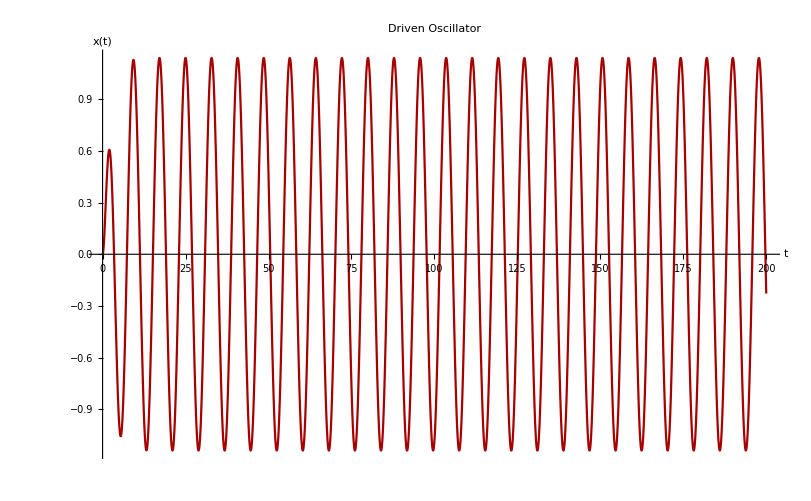

```mathematica
Plot[Evaluate[y[t]/. sol],{t,0,200},PlotLabel->Style["Driven Oscillator",18],AxesLabel->{Style["t",25,Red],Style["x(t)",25,Red]},TicksStyle->Directive[Black,14],AxesStyle->Directive[Black,Thick]]
```

```mathematica
Clear[ω];
```

```mathematica
amplitude[ω_]:=Module[{sol,steady,tvals},
sol=NDSolve[
{y''[t]+2 γ y'[t]+ω0^2 y[t]==(F0/m) Cos[ω t],
y[0]==0,
y'[0]==0},
y,{t,0,200}
];
steady=y/. sol[[1]];
tvals=Range[150,200,0.1]; (* only steady-state oscillation *)
Max[Abs[steady/@tvals]]]
```

steady/@tvals : gives the numerical value of the solution at time tvals .

The steady-state solution of the form:  x(t)≈A(ω)cos(ωt−δ) .

For each driving frequency ω , A(ω) = maximum steady-state displacement .

A(ω)=(F_0/m)/(√((ω_0^2-ω^2)^2 + (2γ ω)^2))

```mathematica
resCurve=Table[{ω,amplitude[ω]},{ω,0.2,2,0.05}]
```

{{0.2,1.01977},{0.25,1.03065},{0.3,1.04364},{0.35,1.05851},{0.4,1.07483},{0.45,1.09206},{0.5,1.1094},{0.55,1.1258},{0.6,1.1399},{0.65,1.1501},{0.7,1.15462},{0.75,1.1517},{0.8,1.1399},{0.85,1.11838},{0.9,1.08715},{0.95,1.04713},{1.,1.},{1.05,0.947875},{1.1,0.892959},{1.15,0.837265},{1.2,0.782397},{1.25,0.729534},{1.3,0.679448},{1.35,0.632579},{1.4,0.589091},{1.45,0.54897},{1.5,0.512147},{1.55,0.478392},{1.6,0.447498},{1.65,0.41924},{1.7,0.39338},{1.75,0.3697},{1.8,0.347995},{1.85,0.32792},{1.9,0.309756},{1.95,0.292887},{2.,0.277349}}

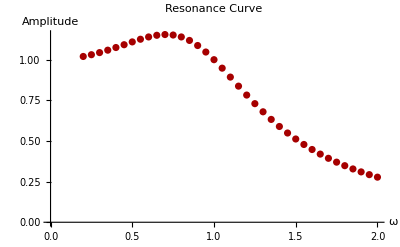

```mathematica
ListPlot[resCurve,PlotLabel->"Resonance Curve",AxesLabel->{Style["ω",18,Red],Style["Amplitude",18,Red]}]
```

The numerical steady-state oscillation amplitude of a damped driven harmonic oscillator as a function of ω. At ω≈ω_0 , there is a resonance.

But, the actual resonance frequency :  ω_r=√(ω_0^2-2 γ^2).

If  γ>0  , the  ω_r<ω_0 .

This means the damping shifts the resonance peak to lower frequency. (slow response)

```mathematica
Manipulate[
Module[{amp,ωr},
ωr=If[ω0^2-2 γ^2>0,Sqrt[ω0^2-2 γ^2],0];
amp[ω_]:=(F0/m)/Sqrt[(ω0^2-ω^2)^2+(2 γ ω)^2];
Plot[amp[ω],{ω,0,2 ω0},
PlotRange->All,
PlotStyle->Thick,
AxesLabel->{Style["ω",18,Red],Style["A(ω)",18,Red]},PlotLabel->Style[Row[{"Resonance Curve   ","ωr = ",NumberForm[ωr,{3,2}]}],16],Epilog->{Blue,Dashed,Line[{{ω0,0},{ω0,5}}],Red,Thick,Line[{{ωr,0},{ωr,5}}]}]],{{γ,0.05,"Damping γ"},0,1,0.01,Appearance->"Labeled"}
]
```

Blue dashed line → natural frequency ω_0 .
Red line → resonance frequency ω_r .

The steady-state solution can be written using complex notation:

x(t)=Re[(F_0/m)/((ω_0^2-ω^2) + i (2γ ω))e^iωt]

The Phase shift, δ=Arg[(ω_0^2-ω^2) + i (2γ ω)]

z=x+i y ,  tan(δ)=y/x=(2γω)/(ω_0^2-ω^2) .

The phase (δ) must smoothly go from 0 → π .

Power absorbed:  ⟨P⟩=F_0^2/m(2γ ω^2)/((ω_0^2-ω^2)^2 + (2γ ω)^2).

Maximum power occurs near resonance.

```mathematica
Manipulate[
Module[{A,phase,ωr,power},
A[ω_]:=(F0/m)/Sqrt[(ω0^2-ω^2)^2+(2 γ ω)^2];
phase[ω_]:=Arg[(ω0^2-ω^2)+I 2 γ ω];
ωr=If[ω0^2-2 γ^2>0,Sqrt[ω0^2-2 γ^2],0];
power[ω_]:=(F0^2/m) (2 γ ω^2)/((ω0^2-ω^2)^2+(2 γ ω)^2);
Grid[{
{Plot[A[ω],{ω,0,2 ω0},PlotLabel->"Amplitude",AxesLabel->{Style["ω",16,Red],Style["A(ω)",16,Red]},PlotStyle->Thick,Epilog->{Red,Dashed,Line[{{ωr,0},{ωr,5}}]}]},{Plot[phase[ω],{ω,0,2 ω0},PlotLabel->"Phase Shift δ(ω)",AxesLabel->{Style["ω",16,Red],Style["δ",16,Red]},PlotRange->{0,Pi},PlotStyle->Blue,Epilog->{Dashed,Black,Line[{{0,Pi/2},{2 ω0,Pi/2}}]}]},{Plot[power[ω],{ω,0,2 ω0},PlotLabel->"Average Power Absorbed",PlotRange->All,AxesLabel->{Style["ω",16,Red],Style["Power",16,Red]},PlotStyle->Darker[Green]]}
}]
],
{{γ,0.1,"Damping γ"},0.01,0.8,0.01,Appearance->"Labeled"}]
```

Plot::plln: Limiting value 2 ω0 in {ω,0,2 ω0} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

```mathematica
z=If[x>0,"Positive","Negative or Zero"]; (* If[condition,truePart,falsePart] *)
```

```mathematica
z/.x->1
```

Positive

Epilog: Additional graphical objects, which draw extra graphics on the main plot.

## 2. Driven Oscillations using RK2 and RK4

We now solve the same system using RK2 and RK4 methods.

Convert into first order equations  (matrix form)

d/dt(x
v)=(v
-2ℽ v-ω_0^2 x +F_0/m cos(ω t))   , where v=d/dt x .

```mathematica
ω=0.8;
```

```mathematica
f[t_,{x_,v_}]:={v,-2 γ v-ω0^2 x+(F0/m) Cos[ω t]};
```

```mathematica
x0={0,0};
```

```mathematica
RK2[f_,y0_,{t0_,tmax_},h_]:=
Module[{tlist,ylist,nsteps,k1},
tlist=Range[t0,tmax,h];
nsteps=Length[tlist];
ylist=ConstantArray[0,nsteps];
ylist[[1]]=y0;

Do[
k1=f[tlist[[n]],ylist[[n]]];
ylist[[n+1]]=ylist[[n]]+h f[tlist[[n]]+(h/2),ylist[[n]]+(h/2) k1];,
{n,1,nsteps-1}
];
Transpose[{tlist,ylist}]
]
```

```mathematica
solRK2=RK2[f,x0,{0,200},0.5];
```

```mathematica
yRK2=Transpose[{solRK2[[All,1]],solRK2[[All,2,1]]}];
```

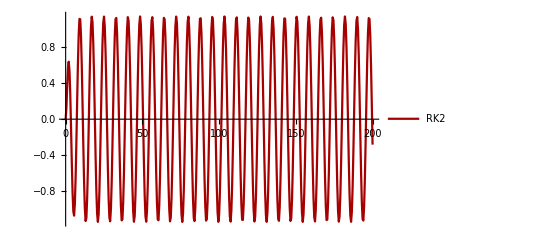

```mathematica
ListLinePlot[{yRK2},PlotLegends->{"RK2"},PlotRange->All]
```

```mathematica
RK4[f_,y0_,{t0_,tmax_},h_]:=
Module[{tlist,ylist,nsteps,k1,k2,k3,k4},
tlist=Range[t0,tmax,h];
nsteps=Length[tlist];
ylist=ConstantArray[0,nsteps];
ylist[[1]]=y0;

Do[
k1=f[tlist[[n]],ylist[[n]]];
k2=f[tlist[[n]]+h/2,ylist[[n]]+h/2 k1];
k3=f[tlist[[n]]+h/2,ylist[[n]]+h/2 k2];
k4=f[tlist[[n]]+h,ylist[[n]]+h k3];
ylist[[n+1]]=ylist[[n]]+(h/6) (k1+2 k2+2 k3+k4),
{n,1,nsteps-1}
];
Transpose[{tlist,ylist}]
]
```

```mathematica
solRK4=RK4[f,x0,{0,200},0.5];
```

```mathematica
yRK4=Transpose[{solRK4[[All,1]],solRK4[[All,2,1]]}];
```

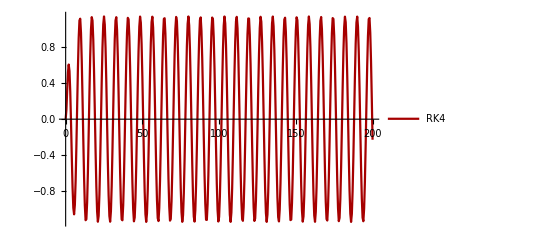

```mathematica
ListLinePlot[{yRK4},PlotLegends->{"RK4"},PlotRange->All]
```

Example 1: A vertically falling object with quartic drag force.

We consider a body of mass m falling under gravity g with a drag force . The equation of motion is:

Let’s define dimensionless variables τ (time) and χ (distance) using the scales provided: τ=t/t_c , χ=y/y_c , where
Time Scale:  
Distance Scale:

dimensionless ODE:     .

We split the second-order ODE into a system of two first-order ODEs:

```mathematica
1.     ,   2.    dv/dτ==1-v^4
```

```mathematica
f[τ_,{χ_,v_}]:={v,1-v^4};
```

```mathematica
nMax=200;
τmax=1;
h=N[τmax/nMax]
```

0.005

```mathematica
x0={0,0};
```

```mathematica
solRK4=RK4[f,x0,{0,1},h];
```

```mathematica
χRK4=Transpose[{solRK4[[All,1]],solRK4[[All,2,1]]}];
```

```mathematica
χAtτ1=χRK4[[-1,2]] (*χ(τ=1)*)
```

0.473244

This is the dimensionless distance at time τ = 1.

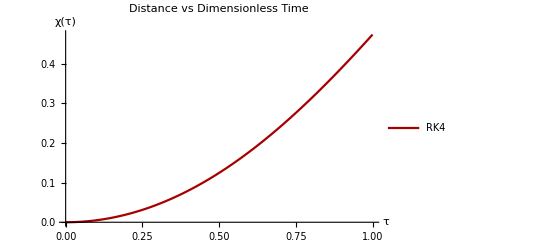

```mathematica
ListLinePlot[{χRK4},PlotLegends->{"RK4"},AxesLabel->{Style["τ",18,Red],Style["χ(τ)",18,Red]},PlotLabel->"Distance vs Dimensionless Time",PlotRange->All]
```

```mathematica
ClearAll["Global`*"];

nMax=300;
τmax=1;
h=N[τmax/nMax];

τ=0;
χ=0;
v=0;

data={};

Do[
AppendTo[data,{τ,χ,v}];
k1χ=v;
k1v=1-v^4;

k2χ=v+(h/2) k1v;
k2v=1-(v+(h/2) k1v)^4;

k3χ=v+(h/2) k2v;
k3v=1-(v+(h/2) k2v)^4;

k4χ=v+h k3v;
k4v=1-(v+h k3v)^4;

χ=χ+(h/6) (k1χ+2 k2χ+2 k3χ+k4χ);
v=v+(h/6) (k1v+2 k2v+2 k3v+k4v);
τ=τ+h;
,{nMax}
];
```

```mathematica
χfinal=χ
```

0.473244

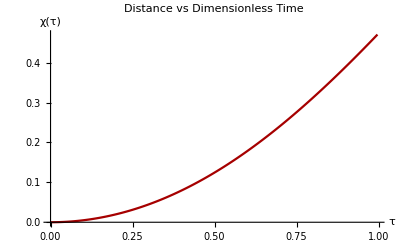

```mathematica
ListLinePlot[data[[All,{1,2}]],AxesLabel->{Style["τ",18,Red],Style["χ(τ)",18,Red]},PlotLabel->"Distance vs Dimensionless Time"]
```

Example 2: A harmonic oscillator is subjected to an external force.

The non-dimensionalized differential equation for a harmonic oscillator driven by a force proportional to t^3:

(d^2 x)/(d t^2)+x==t^3

```mathematica
ClearAll["Global`*"]

f1[t_,x1_,x2_]:=x2
f2[t_,x1_,x2_]:=-x1+t^3

t0=0;
tmax=5;
nMax=300;
h=N[(tmax-t0)/nMax];

t=t0;
x1=0;(*x(t0)*)
x2=0;(*x'(t0)*)


Do[

k1x1=h f1[t,x1,x2];
k1x2=h f2[t,x1,x2];

k2x1=h f1[t+h/2,x1+k1x1/2,x2+k1x2/2];
k2x2=h f2[t+h/2,x1+k1x1/2,x2+k1x2/2];

k3x1=h f1[t+h/2,x1+k2x1/2,x2+k2x2/2];
k3x2=h f2[t+h/2,x1+k2x1/2,x2+k2x2/2];

k4x1=h f1[t+h,x1+k3x1,x2+k3x2];
k4x2=h f2[t+h,x1+k3x1,x2+k3x2];

x1=x1+(k1x1+2 k2x1+2 k3x1+k4x1)/6;
x2=x2+(k1x2+2 k2x2+2 k3x2+k4x2)/6;

t=t+h;
,{nMax}]
```

```mathematica
xATt5=x1
```

89.2465

```mathematica
f[t_,{x1_,x2_}]:={x2,-x1+t^3};
```

```mathematica
x0={0,0};
```

```mathematica
nMax=300;
tmax=5;
h=N[tmax/nMax]
```

0.0166667

```mathematica
solRK4=RK4[f,x0,{0,5},h];
```

```mathematica
x1RK4=Transpose[{solRK4[[All,1]],solRK4[[All,2,1]]}];
```

```mathematica
x1At5=x1RK4⟦-1,2⟧
```

89.2465

```mathematica
Quit[];
```

```mathematica
solExact=DSolve[{x''[t]+x[t]==t^3,x[0]==0,x'[0]==0},x[t],t]
```

{{x[t]→-6 t+t^3+6 Sin[t]}}

```mathematica
N[x[t]/. solExact[[1]]/. t->5]
```

89.2465

Example 3: A projectile motion.

We solve the non-dimensional equation:      with x(0)=1 and initial velocity equal to 1.5 times the escape velocity.

First, we calculate the escape velocity:

E=1/2 v_e^2-1/x=0 (for escape velocity). At x=1, v_e=√2.

```mathematica
ClearAll["Global`*"]

f1[t_,x1_,x2_]:=x2
f2[t_,x1_,x2_]:=-1/x1^2

t0=0;
tmax=2;
nMax=300;
h=(tmax-t0)/nMax;


t=t0;
x1=1;(*x(t0)*)
x2=1.5 Sqrt[2];(* 1.5× escape velocity *)

Do[
k1x1=h f1[t,x1,x2];
k1x2=h f2[t,x1,x2];

k2x1=h f1[t+h/2,x1+k1x1/2,x2+k1x2/2];
k2x2=h f2[t+h/2,x1+k1x1/2,x2+k1x2/2];

k3x1=h f1[t+h/2,x1+k2x1/2,x2+k2x2/2];
k3x2=h f2[t+h/2,x1+k2x1/2,x2+k2x2/2];

k4x1=h f1[t+h,x1+k3x1,x2+k3x2];
k4x2=h f2[t+h,x1+k3x1,x2+k3x2];

x1=x1+(k1x1+2 k2x1+2 k3x1+k4x1)/6;
x2=x2+(k1x2+2 k2x2+2 k3x2+k4x2)/6;
t=t+h;
,{nMax}]
```

```mathematica
xATt2=x1
```

4.63998

Example 4: Van der Pol oscillator

Not all systems return to equilibrium. The nonlinear dynamics for the Van der Pol oscillator is described by

(d^2 x)/dt^2-μ(1-x^2)(d x)/dt+x=0

This can be written as a set of coupled equations:

(d v)/dt=μ(1-x^2) v -x ,
v=(d x)/dt,

```mathematica
mu = 1.0;
```

```mathematica
f[t_,{x_,v_}]:={v,mu (1-x^2) v-x};
```

```mathematica
x0={0.2,0};(*{x(0),v(0)}*)
```

```mathematica
h=0.1;
solRK2=RK2[f,x0,{0,50},h];
```

```mathematica
phaseData=solRK2[[All,2]];
```

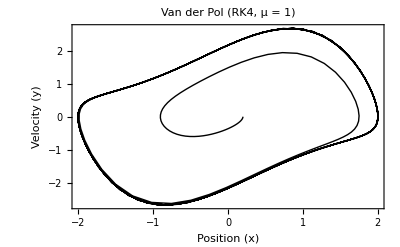

```mathematica
ListLinePlot[phaseData,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"Position (x)","Velocity (y)"},PlotLabel->"Van der Pol (RK4, μ = 1)"]
```

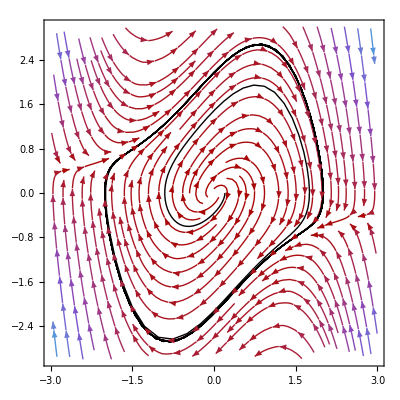

```mathematica
field=StreamPlot[{v,mu (1-x^2) v-x},{x,-3,3},{v,-3,3},StreamStyle->Arrowheads[0.02]];
Show[field,ListLinePlot[phaseData,PlotStyle->{Black,Thick}]]
```

Limit Cycle: A closed, isolated trajectory in phase space. It is a self-sustained periodic motion and it does NOT depend on initial conditions.

Solve using NDSolve:

```mathematica
Quit[];
```

```mathematica
vdp={x'[t]==v[t],v'[t]==mu (1-x[t]^2) v[t]-x[t]};
```

```mathematica
solutions=Table[NDSolveValue[{vdp,x[0]==ic[[1]],v[0]==ic[[2]]},{x[t],v[t]},{t,0,40}],{ic,{{0.1,0},{3,0},{-2,1}}}];
```

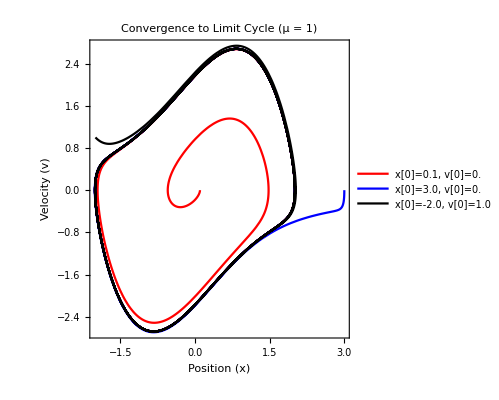

```mathematica
ParametricPlot[Evaluate[solutions],{t,0,40},PlotStyle->{Red,Blue,Black},Frame->True,FrameLabel->{"Position (x)","Velocity (v)"},PlotLabel->"Convergence to Limit Cycle (μ = 1)",PlotLegends->{"x[0]=0.1, v[0]=0.","x[0]=3.0, v[0]=0.","x[0]=-2.0, v[0]=1.0"}]
```

```mathematica
Manipulate[
Module[{vdp,solutions,field},
vdp={x'[t]==v[t],v'[t]==mu (1-x[t]^2) v[t]-x[t]};
solutions=Table[NDSolveValue[{vdp,x[0]==ic[[1]],v[0]==ic[[2]]},{x[t],v[t]},{t,0,50}],{ic,{{0.1,0.1},{2.5,2.5},{-2.5,-0.5}}}];
field=StreamPlot[{v,mu (1-x^2) v-x},{x,-3,3},{v,-3,3},StreamStyle->Arrowheads[0.02],StreamColorFunction->"Rainbow"];
Show[field,ParametricPlot[Evaluate[solutions],{t,0,50},PlotStyle->{Red,Blue,Black}],FrameLabel->{"Position (x)","Velocity (v)"},PlotLabel->Style["Phase Space & Limit Cycles",14]]],{{mu,1.0,"Nonlinearity (μ)"},0.,4.0},SaveDefinitions->True]
```

If  μ=0 , its a pure harmonic oscillator (no limit cycle).